# Wick Contractions

Consider an action S(ϕ)=∫d^d x((∂ϕ)^2+∑_(n=3)^∞ λ_n/(n!)ϕ^n). We want to calculate correlation functions of the type ⟨ϕ(k_1)···ϕ(k_m)⟩.

## Functions and Notation

```mathematica
wick[X_Times]:=Block[{list=List@@X},∑_(j=2)^Length[list] ⟨list[[1]]list[[j]]⟩wick[Times@@Drop[Drop[list,{j}],1]]]
wick[ϕ[a_]ϕ[b_]]:=⟨ϕ[a]ϕ[b]⟩
```

#### Example

```mathematica
wick[ϕ[Subscript[k, 1]]ϕ[Subscript[k, 2]]ϕ[Subscript[k, 3]]ϕ[Subscript[k, 4]]]
```

⟨ϕ[k_2] ϕ[k_3]⟩ ⟨ϕ[k_1] ϕ[k_4]⟩+⟨ϕ[k_1] ϕ[k_3]⟩ ⟨ϕ[k_2] ϕ[k_4]⟩+⟨ϕ[k_1] ϕ[k_2]⟩ ⟨ϕ[k_3] ϕ[k_4]⟩

```mathematica
wick[ϕ[Subscript[k, 1]]ϕ[Subscript[k, 2]]Vertex[4]]
```

(⟨ϕ[k_α$18868[1]] ϕ[k_α$18868[2]]⟩ ⟨ϕ[k_2] ϕ[k_α$18868[3]]⟩+⟨ϕ[k_2] ϕ[k_α$18868[2]]⟩ ⟨ϕ[k_α$18868[1]] ϕ[k_α$18868[3]]⟩+⟨ϕ[k_2] ϕ[k_α$18868[1]]⟩ ⟨ϕ[k_α$18868[2]] ϕ[k_α$18868[3]]⟩) ⟨ϕ[k_1] ϕ[k_α$18868[4]]⟩+⟨ϕ[k_1] ϕ[k_α$18868[3]]⟩ (⟨ϕ[k_α$18868[1]] ϕ[k_α$18868[2]]⟩ ⟨ϕ[k_2] ϕ[k_α$18868[4]]⟩+⟨ϕ[k_2] ϕ[k_α$18868[2]]⟩ ⟨ϕ[k_α$18868[1]] ϕ[k_α$18868[4]]⟩+⟨ϕ[k_2] ϕ[k_α$18868[1]]⟩ ⟨ϕ[k_α$18868[2]] ϕ[k_α$18868[4]]⟩)+⟨ϕ[k_1] ϕ[k_α$18868[2]]⟩ (⟨ϕ[k_α$18868[1]] ϕ[k_α$18868[3]]⟩ ⟨ϕ[k_2] ϕ[k_α$18868[4]]⟩+⟨ϕ[k_2] ϕ[k_α$18868[3]]⟩ ⟨ϕ[k_α$18868[1]] ϕ[k_α$18868[4]]⟩+⟨ϕ[k_2] ϕ[k_α$18868[1]]⟩ ⟨ϕ[k_α$18868[3]] ϕ[k_α$18868[4]]⟩)+⟨ϕ[k_1] ϕ[k_α$18868[1]]⟩ (⟨ϕ[k_α$18868[2]] ϕ[k_α$18868[3]]⟩ ⟨ϕ[k_2] ϕ[k_α$18868[4]]⟩+⟨ϕ[k_2] ϕ[k_α$18868[3]]⟩ ⟨ϕ[k_α$18868[2]] ϕ[k_α$18868[4]]⟩+⟨ϕ[k_2] ϕ[k_α$18868[2]]⟩ ⟨ϕ[k_α$18868[3]] ϕ[k_α$18868[4]]⟩)+⟨ϕ[k_1] ϕ[k_2]⟩ (⟨ϕ[k_α$18868[2]] ϕ[k_α$18868[3]]⟩ ⟨ϕ[k_α$18868[1]] ϕ[k_α$18868[4]]⟩+⟨ϕ[k_α$18868[1]] ϕ[k_α$18868[3]]⟩ ⟨ϕ[k_α$18868[2]] ϕ[k_α$18868[4]]⟩+⟨ϕ[k_α$18868[1]] ϕ[k_α$18868[2]]⟩ ⟨ϕ[k_α$18868[3]] ϕ[k_α$18868[4]]⟩)

## Computing the Wick Contractions

First, note that subscripts are very dangerous!

```mathematica
Subscript[k, 1]//FullForm
```

Subscript[k,1]

```mathematica
D[Subscript[k, 1],k]
```

Subscript^(1,0)[k,1]

This can be fixed with the notation package

```mathematica
<<Notation`
```

```mathematica
Notation[Subscript[k, i_] ⟺ k[i_]]
```

```mathematica
Subscript[k, 1]//FullForm
```

k[1]

```mathematica
D[Subscript[k, 1],k]
```

0

A general vertex will of the form

```mathematica
Vertex[n_]:=Block[{letter=Unique[α]},∏_(j=1)^n ϕ[Subscript[k, letter[j]]]]
```

Now consider an example of a term we may want to Wick contract

```mathematica
towick=ϕ[Subscript[k, 1[]]]ϕ[Subscript[k, 2[]]]Vertex[4] Vertex[4];
EvenQ@Count[towick,ϕ[_]]
```

True

```mathematica
wickcontracted=Expand@wick@towick
```

⟨ϕ[k_α$6224[3]] ϕ[k_α$6224[4]]⟩ ⟨ϕ[k_α$6224[2]] ϕ[k_α$6225[1]]⟩ ⟨ϕ[k_α$6224[1]] ϕ[k_α$6225[2]]⟩ ⟨ϕ[k_(2[])] ϕ[k_α$6225[3]]⟩ ⟨ϕ[k_(1[])] ϕ[k_α$6225[4]]⟩+1+941+1+⟨ϕ[k_(1[])] ϕ[k_(2[])]⟩ 3 ⟨ϕ[k_α$6225[3]] ϕ[k_1]⟩
 |  |  |  |

```mathematica
Length[wickcontracted]
```

945

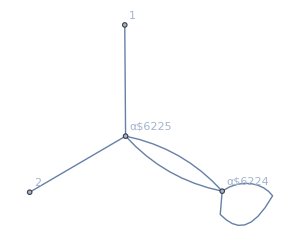

```mathematica
List@@wickcontracted[[1]]/.⟨ϕ[k[a_]]ϕ[k[b_]]⟩:>(a[[0]]-> b[[0]])//GraphPlot[#,VertexLabeling->True,ImageSize->300]&
```

## Plotting the Graphs

Mathematica is very good at drawing general graphs

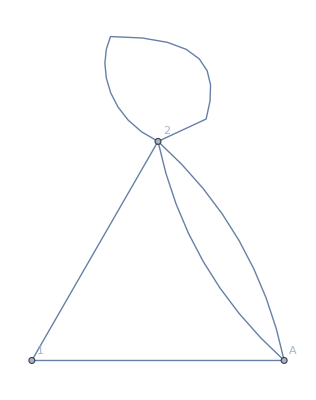

```mathematica
GraphPlot[{1->2,2->A,2->A,2->2,A->1}, VertexLabeling-> True]
```

However, it is very bad at manipulating graphs

```mathematica
Graph[{1->2,2->A,2->A,2->2,A->1}]
```

-Graphics-

```mathematica
Graph[{1->2,2->A,2->A,2->2,A->1}]//ConnectedGraphQ
```

True

Well, apparently this has changed dramatically with the new versions of Mathematica.